```mathematica
mat={{(ϵ^2+2 t1 ϵ ξ)/(t1 t2 ξ),(ϵ+t1 ξ)/(t1 ξ)},{(ϵ+t1 ξ)/(-t1 ξ),-t2/(t1 ξ)}}/.{ξ-> (2 t1 t2 Cos[k]-2 t1 ϵ)/(ϵ^2-t2^2)}//Simplify
```

{{(ϵ (-4 t1^2 ϵ-t2^2 ϵ+ϵ^3+4 t1^2 t2 Cos[k]))/(2 t1^2 t2 (-ϵ+t2 Cos[k])),(ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k]))},{(-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k])),(t2 (t2^2-ϵ^2))/(2 t1^2 (-ϵ+t2 Cos[k]))}}

```mathematica
Eigenvalues[{{(ϵ (-4 t1^2 ϵ-t2^2 ϵ+ϵ^3+4 t1^2 t2 Cos[k]))/(2 t1^2 t2 (-ϵ+t2 Cos[k])),(ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k]))},{(-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k])),(t2 (t2^2-ϵ^2))/(2 t1^2 (-ϵ+t2 Cos[k]))}}]//Simplify
```

{1/(4 t1^2 t2 (-ϵ+t2 Cos[k]))(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2)),1/(4 t1^2 t2 (-ϵ+t2 Cos[k]))(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))}

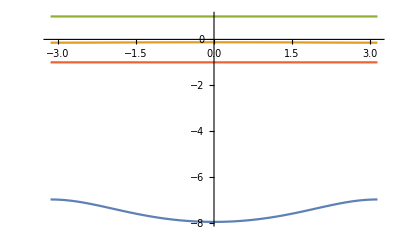

```mathematica
With[{t1=1,t2=.5,ϵ=-1},Plot[{1/(4 t1^2 t2 (-ϵ+t2 Cos[k]))(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2)),1/(4 t1^2 t2 (-ϵ+t2 Cos[k]))(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2)),1,-1},{k,-π,π}]]
```

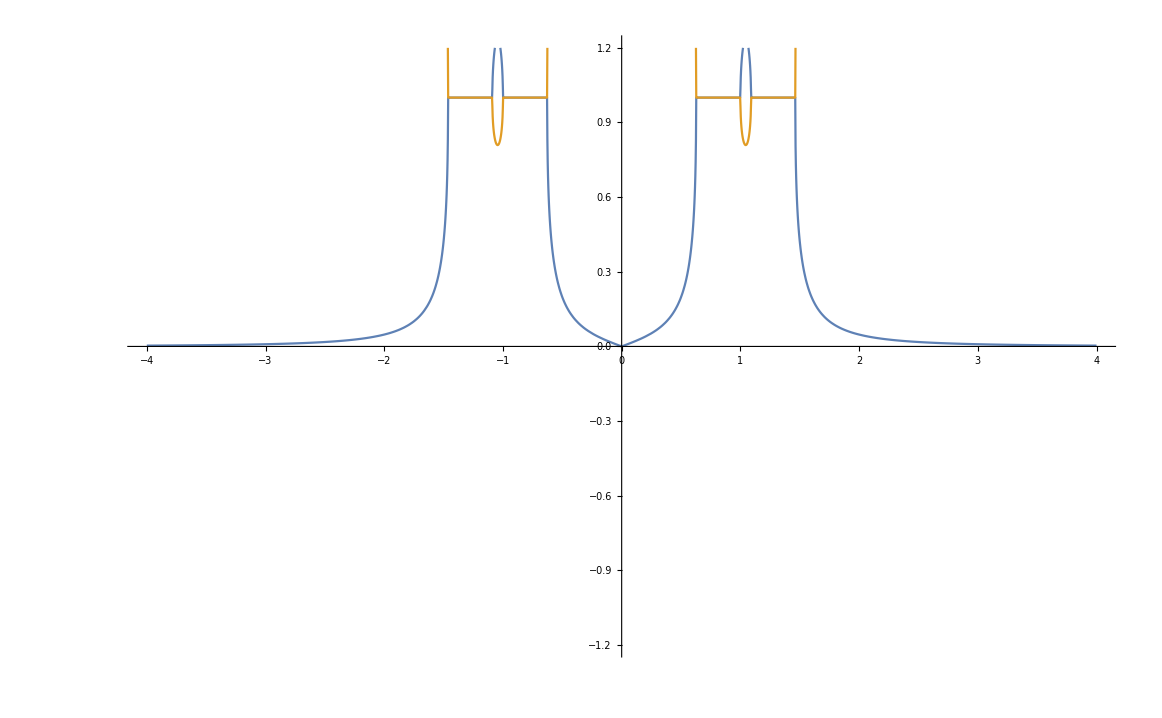

```mathematica
With[{t1=.3,t2=1,k=π/2},Plot[{Abs[1/(4 t1^2 t2 (-ϵ+t2 Cos[k]))(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))],Abs[1/(4 t1^2 t2 (-ϵ+t2 Cos[k]))(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))]},{ϵ,-4,4},PlotRange-> {-1.2,1.2}]]
```

```mathematica
Eigensystem[{{(ϵ (-4 t1^2 ϵ-t2^2 ϵ+ϵ^3+4 t1^2 t2 Cos[k]))/(2 t1^2 t2 (-ϵ+t2 Cos[k])),(ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k]))},{(-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k])),(t2 (t2^2-ϵ^2))/(2 t1^2 (-ϵ+t2 Cos[k]))}}]//Simplify
```

{{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))},{{-(t2^4+4 t1^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])),1},{(-t2^4-4 t1^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])),1}}}

```mathematica
Det[{{-(t2^4+4 t1^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])),1},{ϵ,-t2}}]//Simplify
```

(t2^4-2 t2^2 ϵ^2+ϵ^4+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k])

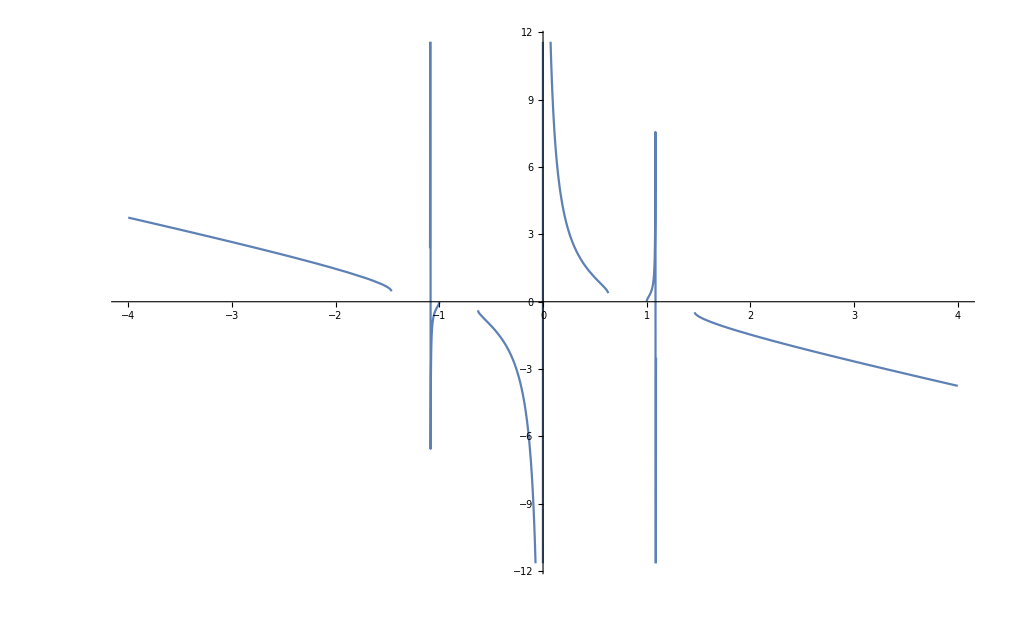

```mathematica
With[{t1=.3,t2=1,k=π/2},Plot[(t2^4-2 t2^2 ϵ^2+ϵ^4+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k]),{ϵ,-4,4}]]
```

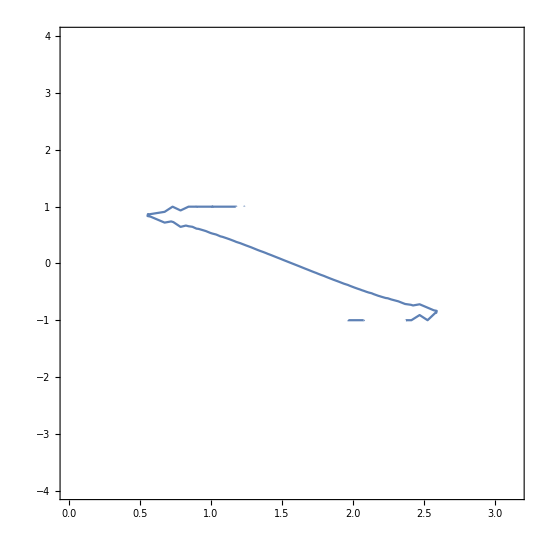

```mathematica
With[{t1=0.1,t2=1},ContourPlot[(t2^4-2 t2^2 ϵ^2+ϵ^4-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k])==0,{k,0,π},{ϵ,-4,4}]]
```